```mathematica
n=3;
gx=0.8;
h=0.1;
```

```mathematica
(*Defining σ and sx Pauli Matrices*)
```

```mathematica
sz[i_]:=Module[{R=ReplacePart[Table[IdentityMatrix[2],n],i->PauliMatrix[3]]},
Return[KroneckerProduct@@R]]
```

```mathematica
sx[i_]:=Module[{R=ReplacePart[Table[IdentityMatrix[2],n],i->PauliMatrix[1]]},
Return[KroneckerProduct@@R]]
```

```mathematica
(*Defining Hilbert-Schmidt norm*)
```

```mathematica
HS[A_]:=Tr[Transpose[Conjugate[A]].A]
```

```mathematica
(*Defining the commutator*)
```

```mathematica
Comm[A_,B_]:=A.B-B.A
```

```mathematica
(*Defining the LMG hamiltonian*)
```

```mathematica
H=-h*Sum[sz[j],{j,1,n}]-(gx/n)*Sum[sx[j],{j,1,n}]*Sum[sx[j],{j,1,n}];
```

```mathematica
(*Choosing A=sx[1] e B=sx[n]*)
```

```mathematica
A[t_]:=MatrixExp[I*t*H].sz[1].MatrixExp[-I*t*H]
B=sz[n];
```

```mathematica
(*Finally, defining ||[A(t),B]|| *)
```

```mathematica
F[t_]:=HS[Comm[A[t],B]]
```

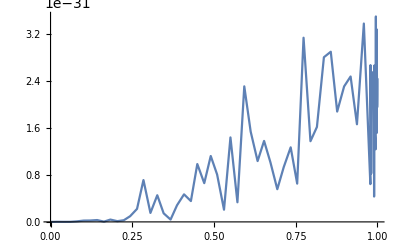

```mathematica
Plot[F[t],{t,0,1}]
```